# FC: Pearson on MI in time

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
dir ="../AnalysisData/best_categ_pass_agent/";
```

```mathematica
aa=Flatten[Import[StringJoin[dir,"fc_corr_mi_A_avoid.dat"]]];
ac=Flatten[Import[StringJoin[dir,"fc_corr_mi_A_pass.dat"]]];
ba=Flatten[Import[StringJoin[dir,"fc_corr_mi_B_avoid.dat"]]];
bc=Flatten[Import[StringJoin[dir,"fc_corr_mi_B_catch.dat"]]];
```

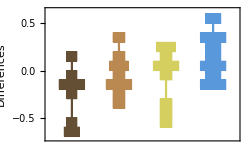

SubtaskCosFC_hist.eps

```mathematica
DistributionChart[{ba-bc,aa-ac,ba-aa,bc-ac},ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",PlotRange->All,FrameLabel->{"","Differences"},Frame->True,ImageSize->250]
Export["SubtaskCosFC_hist.eps",%]
```

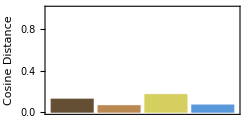

SubtaskCosFC.eps

```mathematica
BarChart[{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Cosine Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},{0.0,1.0}},Frame->True,ImageSize->250]
Export["SubtaskCosFC.eps",%]
```

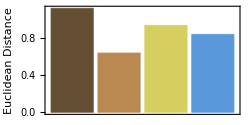

SubtaskEucFC.eps

```mathematica
BarChart[{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Euclidean Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},All},Frame->True,ImageSize->250]
Export["SubtaskEucFC.eps",%]
```